```mathematica
D[1/Cosh[x/a]^2, x]
```

-(2 Sech[x/a]^2 Tanh[x/a])/a

```mathematica
DSolve[{f'[x]==(-Cos[γ+θ[x]])/f[x]^2, θ'[x]==(-Sin[γ+θ[x]])/f[x]^2}, {f[x], θ[x]}, x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ[x]→-γ+ArcSin[ⅇ^(C[1]+InverseFunction[-(√(1-ⅇ^(-2 (C[1]+#1))) (2 HypergeometricPFQ[{1/2,1/2,1/2,1/2},{3/2,3/2,3/2},ⅇ^(-2 (C[1]+#1))]+2 HypergeometricPFQ[{1/2,1/2,1/2},{3/2,3/2},ⅇ^(-2 (C[1]+#1))] #1+ⅇ^(C[1]+#1) ArcSin[ⅇ^(-C[1]-#1)] #1^2))/(√(1-ⅇ^(2 (C[1]+#1))))&][-x+C[2]])],f[x]→InverseFunction[-1/(√(1-ⅇ^(2 (C[1]+#1))))√(1-ⅇ^(-2 (C[1]+#1))) (2 HypergeometricPFQ[{1/2,1/2,1/2,1/2},{3/2,3/2,3/2},ⅇ^(-2 (C[1]+#1))]+2 HypergeometricPFQ[{1/2,1/2,1/2},{3/2,3/2},ⅇ^(-2 (C[1]+#1))] #1+ⅇ^(C[1]+#1) ArcSin[ⅇ^(-C[1]-#1)] #1^2)&][-x+C[2]]}}

```mathematica
DSolve[I θ'[x]==-ϵ^(I(γ+θ[x])), θ[x], x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ[x]→(ⅈ Log[ⅈ (-ⅈ x ϵ^(ⅈ γ)-C[1]) Log[ϵ]])/Log[ϵ]}}

```mathematica
DSolve[f'[x]==-1/f[x]^2, f[x], x]
```

{{f[x]→-(-3)^(1/3) (-x+C[1])^(1/3)},{f[x]→3^(1/3) (-x+C[1])^(1/3)},{f[x]→(-1)^(2/3) 3^(1/3) (-x+C[1])^(1/3)}}

```mathematica
Series[Tanh[x],{x, 0, 5}]
```

x-x^3/3+(2 x^5)/15+O[x]^6

```mathematica
DSolve[I θ'[x]==-ϵ^(2 I θ[x]), θ[x], x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Reduce::naqs: {θ[x]→(ⅈ Log[2 ⅈ (-ⅈ x-«) Log[ϵ]])/(2 Log[ϵ])} is not a quantified system of equations and inequalities.

Reduce[{{θ[x]→(ⅈ Log[2 ⅈ (-ⅈ x-C[1]) Log[ϵ]])/(2 Log[ϵ])}}]

```mathematica
sol=DSolve[{f'[x]==(-Cos[2θ[x]])/f[x]^2, θ'[x]==(-Sin[2θ[x]])/f[x]^3}, {f[x], θ[x]}, x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ[x]→1/2 ArcSin[ⅇ^(2 C[1]) (InverseFunction[1/3 Hypergeometric2F1[1/2,3/4,7/4,ⅇ^(4 C[1]) #1^4] #1^3&][-x+C[2]])^2],f[x]→InverseFunction[1/3 Hypergeometric2F1[1/2,3/4,7/4,ⅇ^(4 C[1]) #1^4] #1^3&][-x+C[2]]}}

```mathematica
FullSimplify[%/. {C[1]->0, C[2]->0}]
```

{{θ[x]→1/2 ArcSin[(InverseFunction[1/3 Hypergeometric2F1[1/2,3/4,7/4,ⅇ^(4 0) #1^4] #1^3&][-x])^2],f[x]→InverseFunction[1/3 Hypergeometric2F1[1/2,3/4,7/4,ⅇ^(4 0) #1^4] #1^3&][-x]}}

```mathematica
fSol=f[x]/. sol[[1]]
```

InverseFunction[1/3 Hypergeometric2F1[1/2,3/4,7/4,ⅇ^(4 C[1]) #1^4] #1^3&][-x+C[2]]

```mathematica
Plot[fSol,{x,-1,1},PlotLabel->"График f(x)",AxesLabel->{"x","f(x)"},PlotRange->All]
```

-Graphics-

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvsing: Unable to resolve some of the arbitrary constants in the general solution using the given boundary conditions. It is possible that some of the conditions have been specified at a singular point for the equation.

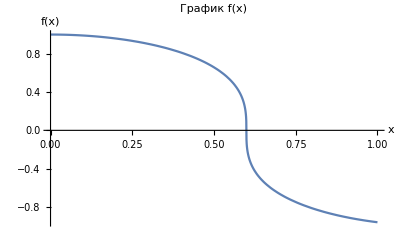

```mathematica
(*Решаем систему*)sol=DSolve[{f'[x]==-Cos[2 θ[x]]/f[x]^2,θ'[x]==-Sin[2 θ[x]]/f[x]^3, f[0]==1,θ[0]==Pi/4},{f[x],θ[x]},x];

(*Извлекаем f(x)*)
fSol=f[x]/. First[sol];
sSol=θ[x]/.sol[[2]];

(*Строим график для конкретных констант*)
Plot[fSol/. {C[1]->0,C[2]->1},{x,-1,1},PlotLabel->"График f(x)",AxesLabel->{"x","f(x)"},PlotRange->All]
```

```mathematica
Series[fSol, {x,0, 2}]
```

InverseFunction[1/3 Hypergeometric2F1[1/2,3/4,7/4,ⅇ^(4 C[1]) #1^4] #1^3&][C[2]]-(√(1-ⅇ^(4 C[1]) (InverseFunction[1/3 Hypergeometric2F1[1/2,3/4,7/4,ⅇ^(4 C[1]) #1^4] #1^3&][C[2]])^4) x)/(InverseFunction[1/3 Hypergeometric2F1[1/2,3/4,7/4,ⅇ^(4 C[1]) #1^4] #1^3&][C[2]])^2-x^2/(InverseFunction[1/3 Hypergeometric2F1[1/2,3/4,7/4,ⅇ^(4 C[1]) #1^4] #1^3&][C[2]])^5+O[x]^3

```mathematica
(*Решаем систему дифференциальных уравнений*)sol=NDSolve[{f'[x]==-Cos[2 θ[x]]/f[x]^2,θ'[x]==-Sin[2 θ[x]]/f[x]^3,f[-10]==1,(*Начальное условие для f(x)*)θ[-10]==0                  (*Начальное условие для θ(x)*)},{f,θ},{x,-10,2}];(*Диапазон по x*)(*Вычисляем вещественную часть*)realPart[x_]:=Re[f[x] Exp[I θ[x]]/. sol[[1]]];
(*Строим график вещественной части*)Plot[realPart[x],{x,-2,2},PlotLabel->"Вещественная часть Re[f(x)exp(iθ(x))]",AxesLabel->{"x","Re[f(x)exp(iθ(x))]"},PlotStyle->Thick,PlotRange->All]
```

NDSolve::ndsz: At x == -9.66667, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-1.99992} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
(*Решаем систему дифференциальных уравнений*)sol=NDSolve[{f'[x]==-Cos[2 θ[x]]/f[x]^2,θ'[x]==-Sin[2 θ[x]]/f[x]^3,f[-10]==1,(*Начальное условие для f(x)*)θ[-10]==1                 (*Начальное условие для θ(x)*)},{f,θ},{x,-10,10}];(*Диапазон по x*)(*Строим график θ(x)*)Plot[θ[x]/. sol,{x,-0.58,0.58},PlotLabel->"График θ(x)",AxesLabel->{"x","θ(x) [радианы]"},PlotStyle->{Thick,Red},GridLines->Automatic,PlotRange->All]
```

NDSolve::ndsz: At x == -9.06541, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-0.579976} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
(*Численное решение системы дифференциальных уравнений*)sol=NDSolve[{f'[x]==-Cos[2 θ[x]]/f[x]^2,θ'[x]==-Sin[2 θ[x]]/f[x]^3,f[0]==1,(*Начальное условие для f(x)*)θ[0]==Pi/4                  (*Начальное условие для θ(x)*)},{f,θ},{x,-1,1}];(*Диапазон интегрирования*)(*Построение графиков решений*)Plot[Evaluate[{f[x],θ[x]}/. sol],{x,-1,1},PlotLabel->"Решения системы ОДУ",AxesLabel->{"x","f(x) и θ(x)"},PlotLegends->{"f(x)","θ(x)"},PlotStyle->{{Thick,Blue},{Thick,Red}},GridLines->Automatic,PlotRange->All]

(*Отдельные графики для каждой функции*)
GraphicsRow[{Plot[f[x]/. sol,{x,-1,1},PlotLabel->"Функция f(x)",AxesLabel->{"x","f(x)"},PlotStyle->{Thick,Blue},GridLines->Automatic],Plot[θ[x]/. sol,{x,-1,1},PlotLabel->"Функция θ(x)",AxesLabel->{"x","θ(x) [рад]"},PlotStyle->{Thick,Red},GridLines->Automatic]}]
```

NDSolve::ndsz: At x == -0.59907, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == 0.59907, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
DSolve[θ'[y]==(-θ[y])/(-3y)^(1/3), θ[y], y]
```

{{θ[y]→ⅇ^(1/2 3^(2/3) (-y)^(2/3)) C[1]}}